## Header

```mathematica
Clear["Global`*"]
Needs["MaTeX`"];
Tex[x_]:=MaTeX[x,Magnification->2];

(*define plot options*)

colors=RGBColor/@{"#000000","#e69f00","#56b4e9","#009e73","#f0e442","#0072b2","#d55e00","#cc79a7"};
markers={"△","▲","□","■","◦","•","◇","◆","▽","▼","▯","▮"};
texStyle={FontFamily->"Latin Modern Math",FontSize->20, Black};
defaultPlotOptions={BaseStyle->texStyle,Frame->True,ImageSize->500,AspectRatio->Full,PlotRange->All,FrameLabel->{"x","y"}};
SetOptions[Plot,Evaluate[defaultPlotOptions],PlotStyle->colors];
SetOptions[ListPlot,Evaluate[defaultPlotOptions],PlotStyle->colors,Joined->True,PlotMarkers->markers];
SetOptions[ContourPlot,Evaluate[defaultPlotOptions],ColorFunction->"TemperatureMap"];
(*export to./notebook_figures/img.pdf*)

exportDir=ParentDirectory[NotebookDirectory[]]<>"/plots/";
export[imgname_,img_]:=Export[exportDir<>imgname<>".pdf",img] (*export to a notebook_figures*)
(*autosave notebook*)

SetOptions[$FrontEndSession,NotebookAutoSave->True];
(*file detail*)
Print[Style["Bibek Pokharel (pokharel@usc.edu)",texStyle]]
Print[Style["Created: "<>ToString[DateString[FileDate[NotebookFileName[],"Creation"]]],texStyle]]
Print[Style["Modified: "<>ToString[DateString[FileDate[NotebookFileName[],"Modification"]]],texStyle]]
NotebookSave[]
```

Bibek Pokharel (pokharel@usc.edu)

Created: Tue 14 Jun 2022 12:00:44

Modified: Tue 14 Jun 2022 18:21:48

## Data Import

```mathematica
dataFiles={"avgtts_cairo_dd-rga32c-rga16b_marks-all_embedding-2.csv","avgtts_cairo_dd-ur18-ur42_marks-all_embedding-2.csv","avgtts_cairo_dd-rga32a-ur38_marks-all_embedding-2.csv","avgtts_montreal_dd-ur14-supercpmg_marks-all_embedding-2.csv","avgtts_montreal_dd-xy4-supereuler_marks-all_embedding-2.csv","avgtts_cairo_dd-xy4-ur10_marks-all_embedding-1.csv"};
baseFiles= Table[ParentDirectory[NotebookDirectory[]]<>"/results/"<>f,{f,dataFiles}];
```

```mathematica
findFilename[machine_, sequence_,embedding_:"2"]:=Module[{chosenFile, seqname},
seqname = StringReplace[StringReplace[sequence, "_"->""], "free"->""];
Do[ If[StringMatchQ[f,"*"<>machine<>"*"<>seqname<>"*"<>"embedding-"<>embedding<>"*"], chosenFile = f], {f, baseFiles}];
chosenFile
]
```

```mathematica
findDataSet[machine_, sequence_,embedding_:"2"]:=Import[ findFilename[machine, sequence, embedding], "CSV"]
```

```mathematica
plotdata[machine_, sequence_,embedding_:"2",start_:1,stop_:26]:=Module[{rawdata, header,column, chosen,newdata, value, error, stopval},
rawdata = findDataSet[machine, sequence,embedding];
header =rawdata[[1]];
column = Position[header,sequence<>" mean"][[1]][[1]];

chosen= rawdata[[2;;, {column, column+1}]];
If[machine=="cairo"&&embedding=="2",stopval=23, stopval=stop];
(*stopval=stop;*)
newdata = {};
Do[
value= chosen[[i]][[1]];
error = chosen[[i]][[2]]; 

If[value!="", 
	AppendTo[newdata, {i, Around[value,5*error]}]
	];
,{i, start,Min[stopval, Length[chosen]]}
];
newdata
]
```

```mathematica
plotdata["montreal", "ur_14","2"]
```

{{1,-5.0480.017},{2,-4.8620.011},{3,-4.7260.009},{4,-4.6230.008},{5,-4.5190.007},{6,-4.4140.007},{7,-4.3110.007},{8,-4.2050.008},{9,-4.0970.008},{10,-3.9810.009},{11,-3.8570.010},{12,-3.7300.012},{13,-3.5910.013},{14,-3.4540.013},{15,-3.3060.014},{16,-3.1470.018},{17,-2.9790.020},{18,-2.8080.024},{19,-2.6350.029},{20,-2.4660.033},{21,-2.300.04},{22,-2.120.05},{23,-1.930.06},{24,-1.740.08},{25,-1.560.09},{26,-1.410.10}}

```mathematica
ListPlot[
{
plotdata["cairo", "ur_18","2"],
plotdata["cairo","free","2"]
}]
```

-Graphics-

```mathematica
durationsCairo = Transpose[Import["/Users/bibekpokharel/Dropbox/dd_on_algorithms_test/results/bv/ibm_cairo/20220412/idealtts_cairo_dd-ur18-ur42_marks-all_cycle-2_run-1.csv","CSV"]][[1]][[2;;]]
durationsMontreal = Transpose[Import["/Users/bibekpokharel/Dropbox/dd_on_algorithms_test/results/bv/ibmq_montreal/20220412/idealtts_montreal_dd-ur14-supercpmg_marks-all_cycle-2_run-1.csv","CSV"]][[1]][[2;;]]
```

{-6.06989,-6.02787,-5.98465,-5.93741,-5.88619,-5.83234,-5.77756,-5.72352,-5.67165,-5.62294,-5.57774,-5.53596,-5.49723,-5.46114,-5.42736,-5.39569,-5.366,-5.33824,-5.31233,-5.28815,-5.26555,-5.24434,-5.22429,-5.20521,-5.18692,-5.16927}

{-5.26106,-5.24578,-5.22562,-5.20112,-5.17514,-5.14978,-5.1259,-5.10349,-5.08225,-5.06183,-5.04202,-5.02273,-5.00397,-4.98578,-4.96824,-4.95143,-4.93539,-4.92017,-4.90578,-4.89219,-4.87936,-4.8672,-4.85562,-4.84453,-4.83383,-4.82344}

```mathematica
restrict[data_, start_, end_:1]:=Module[{n}, 
If[end==1, n=Length[data], n=Min[Length[data],end]];
Table[data[[i]],{i, start,n}]
]
```

```mathematica
nmax[machine_, sequence_, embedding_:"2"]:=Module[{avgDataset, DDdata, len, novals,val},
avgDataset = Import[findFilename[machine, sequence, embedding], "Dataset", "HeaderLines"->1];
DDdata = Normal[avgDataset[All, sequence<>" mean"]];
len = Length[DDdata];
novals = Count[DDdata, ""];
val=len-novals;
If[machine=="cairo"&& sequence=="free"&&embedding=="2", val=20];
If[machine=="cairo"&& sequence!="free"&&embedding=="2", val=23];
val
]
(*nmax["montreal", "ur_14", "2"]*)
```

## Import bootstrapped fits

```mathematica
datanames={{"ibm_cairo","xy4","1"},{"ibm_cairo","free", "1"},{"ibm_cairo","ur_10","1"},{"ibmq_montreal","super_euler","2"},{"ibmq_montreal","ur_14","2"},{"ibmq_montreal","super_cpmg","2"},{"ibmq_montreal","xy4","2"},{"ibmq_montreal","free","2"},{"ibm_cairo","rga32a","2"},{"ibm_cairo","ur_38","2"},{"ibm_cairo","ur_18","2"},{"ibm_cairo","ur_42","2"},{"ibm_cairo","free","2"}};
```

```mathematica
Do[
filename = ParentDirectory[NotebookDirectory[]]<>"/results/"<>"lambda_"<>x[[1]]<>"_"<>x[[2]]<>"_embedding-"<>x[[3]]<>".csv";
lambdaData =Import[filename,"CSV"];
machineShort = StringSplit[x[[1]], "_"][[-1]];
lambdaList[machineShort, x[[2]], x[[3]]]=Table[{x[[1]], Around[x[[2]], x[[3]]]},{x,lambdaData}]
,{x,datanames}]
```

```mathematica
lambdaList["montreal", "ur_14", "2"]
```

{{3,0.5350.010},{4,0.4690.007},{5,0.4310.006},{6,0.4090.005},{7,0.3940.004},{8,0.38370.0032},{9,0.37740.0027},{10,0.37470.0024},{11,0.3990.005},{12,0.4160.005},{13,0.4420.005},{14,0.4600.006},{15,0.4730.007},{16,0.5100.009},{17,0.5430.011},{18,0.5630.012},{19,0.5710.015},{20,0.5690.013},{21,0.5680.014},{22,0.5810.023},{23,0.6090.027},{24,0.630.04},{25,0.6130.032},{26,0.5950.026}}

```mathematica
filename = ParentDirectory[NotebookDirectory[]]<>"/results/worst_fits.csv";
worstFitData=Import[filename, "Dataset", HeaderLines->1]
```

Dataset[<>]

```mathematica
lambda[machine_, seq_, emb_]:=worstFitData[Select[#machine==machine&&#seq==seq&&#embedding==ToExpression[emb]&], {"slope"}][[1]][[1]]
lambdaerr[machine_, seq_, emb_]:=worstFitData[Select[#machine==machine&&#seq==seq&&#embedding==ToExpression[emb]&], {"slope err"}][[1]][[1]]
intercept[machine_, seq_, emb_]:=worstFitData[Select[#machine==machine&&#seq==seq&&#embedding==ToExpression[emb]&], {"intercept"}][[1]][[1]]
intercepterr[machine_, seq_, emb_]:=worstFitData[Select[#machine==machine&&#seq==seq&&#embedding==ToExpression[emb]&], {"intercept err"}][[1]][[1]]
```

```mathematica
ExtractFit[machine_, sequence_, embedding_:"2"]:=Module[{m,dm, k, dk, roundm, rounderr},
{m,dm}={lambda[machine, sequence, embedding],lambdaerr[machine, sequence, embedding]};
roundm= Round[Log2[10]m,0.01];
rounderr=Round[Log2[10]dm,0.01];
If [rounderr==0, roundm= Round[Log2[10]m,0.0001];rounderr= Round[Log2[10]dm,0.0001]];
ToString[roundm]<>" ± "<>ToString[rounderr]
]
```

## Plot Functions

```mathematica
timeMarkers = { {-8, "10 ns"}, {-7, "100 ns"}, {-6, "1 μs"}, {-5, "10 μs"}, {-4, "100 μs"},{-3, "1 ms"},{-2, "10 ms"},{-1, "100 ms"}, {0, "1 s"}};
```

```mathematica
idealfit=Plot[Table[{Log10[2]n+c},{c,{-0.5,-1.5,-2.5,-3.5,-4.5,-5.5, -6.5, -7.5, -8.5, -9.5, -10.5, -11.5, -12.5,-13.5, -14.5}}],{n,1,27}, PlotStyle->{White, Thickness[0.002]},  Frame->True,LabelStyle->texStyle, AspectRatio->0.7, ImageSize->650,PlotRange->{{1,26}, {-7,0.5}}, Prolog->{GrayLevel[0.9],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}];

durationsFitM = ListPlot[ durationsMontreal, PlotMarkers->None, PlotStyle->{{colors[[7]],Dashing[0.03],Thickness[0.003], Opacity[0.5]}, {Black, Dashing[0.03],Thickness[0.003], Opacity[0.5]}},Frame->True,LabelStyle->texStyle,AspectRatio->0.7, ImageSize->650];

durationsFitC= ListPlot[durationsCairo, PlotMarkers->None, PlotStyle->{{colors[[6]],Dashing[0.03],Thickness[0.003], Opacity[0.5]}, {Black, Dashing[0.03],Thickness[0.003], Opacity[0.5]}},Frame->True,LabelStyle->texStyle,AspectRatio->0.7, ImageSize->650];

backgroundC=Show[idealfit,  durationsFitC, FrameLabel->{Tex["n"], "TTS"}, ImageSize->650, AspectRatio->0.7, LabelStyle->texStyle, FrameTicks->{ {2,6,10,14,18,22,26}, timeMarkers,None, None}];

backgroundM=Show[idealfit,  durationsFitM, FrameLabel->{Tex["n"], "TTS"}, ImageSize->650, AspectRatio->0.7, LabelStyle->texStyle, FrameTicks->{ {2,6,10,14,18,22,26}, timeMarkers,None, None}];

background=Show[idealfit, durationsFitM, durationsFitC, FrameLabel->{Tex["n"], "TTS"}, ImageSize->650, AspectRatio->0.7, LabelStyle->texStyle, FrameTicks->{ {2,6,10,14,18,22,26}, timeMarkers,None, None}]
```

-Graphics-

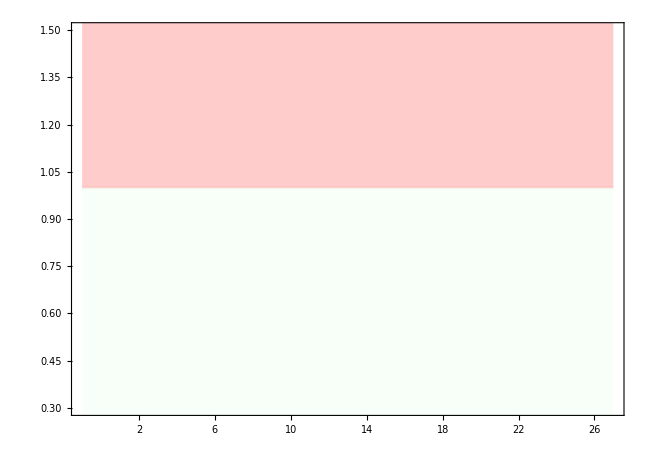

```mathematica
background2 = Show[Plot[1, {x,-1,27}, PlotStyle->{Red,Opacity[0.1]}, Filling->{Top}],
Plot[1, {x,-1,27}, PlotStyle->{LightGreen,Opacity[0.1]}, Filling->{Bottom}], FrameLabel->Tex@{"n", "\\lambda"}, ImageSize->650, AspectRatio->0.7, LabelStyle->texStyle, FrameTicks->{ {2,6,10,14,18,22,26}, Automatic,None, None}, PlotRange->{All, {0.3, 1.5}}]
```

```mathematica
ListPlotWithFit[machine_, sequence_, embedding_,color_, marker_,fitstart_]:=Module[{data,m,c,nofitPlot, fitPlot,fitend},
{m,c}={lambda[machine,sequence,embedding], intercept[machine,sequence,embedding]};
data=plotdata[machine, sequence, embedding];
fitend=data[[-1]][[1]];
nofitPlot=ListPlot[data, PlotStyle->{color, Dotted}, Joined->True, PlotMarkers->marker,IntervalMarkersStyle-><|"FenceStyle"->{color, Dashing[None]}, "WhiskerStyle"->{color, Dashing[None]},"FenceWidth"->0.2|>];
fitPlot=Plot[m x + c, {x,fitstart,fitend}, PlotStyle->{color}];
Show[nofitPlot, fitPlot]

]
```

```mathematica
plotfit = ListPlotWithFit["montreal", "ur_14","2",colors[[8]],markers[[3]], 12];
Show[background, plotfit, PlotRange->{All, {-6,0}}]
```

-Graphics-

## Legends

```mathematica
GetLegends[ nameList_, colorList_, markerList_]:=Module[{labels},
labels = Table[Style[x, texStyle],{x, nameList}];
SwatchLegend[colorList, labels, LegendMarkers->Table[{x,20},{x,markerList}], LegendFunction->(Framed[#,FrameMargins->0,RoundingRadius->4,Background->White, FrameStyle->LightGray]&)]
]
```

```mathematica
GetLegends[{"a", "b"}, {colors[[1]], colors[[2]]}, {markers[[1]], markers[[2]]}]
```

```mathematica
GetLineLegends[ nameList_, colorList_, markerList_]:=Module[{labels},
labels = Table[Style[x, texStyle],{x, nameList}];
LineLegend[colorList, labels, LegendMarkers->Table[{x,20},{x,markerList}], LegendFunction->(Framed[#,FrameMargins->0,RoundingRadius->4,Background->White, FrameStyle->LightGray]&)]
]
```

```mathematica
GetLineLegends[{"a", "b"}, {colors[[1]], colors[[2]]}, {markers[[1]], markers[[2]]}]
```

```mathematica
GetLegends2[ nameList_, colorList_, markerList_]:=Module[{labels},
labels = Table[Style[x, texStyle],{x, nameList}];
SwatchLegend[colorList, labels, LegendMarkers->Table[{x,20},{x,markerList}], LegendFunction->(Framed[#,FrameMargins->0,RoundingRadius->4,Background->White, FrameStyle->LightGray]&), LegendLayout->{"Column",2}]
]
```

```mathematica
GetLineLegends2[ nameList_, colorList_, markerList_]:=Module[{labels},
labels = Table[Style[x, texStyle],{x, nameList}];
LineLegend[colorList, labels, LegendMarkers->Table[{x,20},{x,markerList}], LegendFunction->(Framed[#,FrameMargins->0,RoundingRadius->4,Background->White, FrameStyle->LightGray]&), LegendLayout->{"Column",2}]
]
```

```mathematica
GetLegends2[{"a", "b"}, {colors[[1]], colors[[2]]}, {markers[[1]], markers[[2]]}]
```

## Average comparison - Montreal and Cairo

```mathematica
datanames = {{"montreal", "free", "2" }, {"montreal", "ur_14", "2"}, {"cairo", "free", "2"},{"cairo", "ur_18", "2"} };
plotColors = {colors[[7]],colors[[7]],colors[[6]],colors[[6]]};
plotMarkers ={ markers[[3]],markers[[6]],markers[[7]],markers[[2]]};
plotNames = {"Montreal w/o DD","Montreal w/ DD","Cairo w/o DD","Cairo w/ DD"};
nameLegend = GetLegends[plotNames, plotColors, plotMarkers];
```

### TTS

```mathematica
plotLegendFits = Table[ExtractFit[d[[1]], d[[2]], d[[3]]],{d, datanames}];
fitLegend = GetLineLegends[plotLegendFits, plotColors, plotMarkers]
```

```mathematica
Show[
background,
ListPlotWithFit[datanames[[1]][[1]],datanames[[1]][[2]],datanames[[1]][[3]],plotColors[[1]],plotMarkers[[1]],8],
ListPlotWithFit[datanames[[2]][[1]],datanames[[2]][[2]],datanames[[2]][[3]],plotColors[[2]],plotMarkers[[2]],12],
ListPlotWithFit[datanames[[3]][[1]],datanames[[3]][[2]],datanames[[3]][[3]],plotColors[[3]],plotMarkers[[3]],11],
ListPlotWithFit[datanames[[4]][[1]],datanames[[4]][[2]],datanames[[4]][[3]],plotColors[[4]],plotMarkers[[4]],17],
ListPlot[{},  PlotLegends->{Placed[nameLegend, {0.18,0.8}], Placed[fitLegend, {0.86,0.22}]}],
PlotRange->{{1,27}, {-6.5,0}}, ImageSize->700
]
```

-Graphics-

```mathematica
export["bv_montreal_cairo_tts", %]
```

/Users/bibekpokharel/Dropbox/Research/bv-quantum-speedup/plots/bv_montreal_cairo_tts.pdf

### Lambda

```mathematica
plotDataLambda = Table[lambdaList[d[[1]],d[[2]], d[[3]]],{d,datanames}];
```

```mathematica
Show[background2,
ListPlot[plotDataLambda,
 PlotStyle-> Table[{c, Dotted},{c,plotColors}],
  PlotLegends->Placed[nameLegend, {0.18,0.8}], 
IntervalMarkersStyle-><|"FenceStyle"->{Dashing[None]}, "WhiskerStyle"->{Dashing[None]},"FenceWidth"->0.2|>,PlotMarkers->plotMarkers] ,

 PlotRange->{{2,26}, {0.3, 1.3}}, Axes->False
   
]
```

-Graphics-

```mathematica
export["bv_montreal_cairo_lambda", %]
```

/Users/bibekpokharel/Dropbox/Research/bv-quantum-speedup/plots/bv_montreal_cairo_lambda.pdf

## DD comparison - Montreal

```mathematica
datanames = { {"montreal", "super_euler", "2"}, {"montreal", "ur_14", "2"}, {"montreal", "super_cpmg", "2"}, {"montreal", "xy4", "2"} ,{"montreal", "free", "2"}};
plotColors = {colors[[8]],colors[[4]],colors[[7]],colors[[6]], colors[[3]]};
plotMarkers ={ markers[[4]],markers[[6]],markers[[8]],markers[[2]], markers[[1]]};
plotNames = {"Super Euler","UR 14","Super CPMG","XY4", "Free"};
nameLegend = GetLegends[plotNames, plotColors, plotMarkers];
```

### TTS

```mathematica
plotLegendFits = Table[ExtractFit[d[[1]], d[[2]]],{d, datanames}];
fitLegend = GetLineLegends[plotLegendFits, plotColors, plotMarkers]
```

```mathematica
Show[backgroundM,
ListPlotWithFit[datanames[[1]][[1]],datanames[[1]][[2]],datanames[[1]][[3]],plotColors[[1]],plotMarkers[[1]],12],ListPlotWithFit[datanames[[2]][[1]],datanames[[2]][[2]],datanames[[2]][[3]],plotColors[[2]],plotMarkers[[2]],12],ListPlotWithFit[datanames[[3]][[1]],datanames[[3]][[2]],datanames[[3]][[3]],plotColors[[3]],plotMarkers[[3]],12],
ListPlotWithFit[datanames[[4]][[1]],datanames[[4]][[2]],datanames[[4]][[3]],plotColors[[4]],plotMarkers[[4]],12],
ListPlotWithFit[datanames[[5]][[1]],datanames[[5]][[2]],datanames[[5]][[3]],plotColors[[5]],plotMarkers[[5]],8],ListPlot[{},PlotLegends->{Placed[nameLegend,{0.16,0.77}],Placed[fitLegend,{0.84,0.27}]}],PlotRange->{{1,27},{-6,0}},ImageSize->700]
```

-Graphics-

```mathematica
export["dd_montreal_tts", %]
```

/Users/bibekpokharel/Dropbox/Research/bv-quantum-speedup/plots/dd_montreal_tts.pdf

### Lambda

```mathematica
plotDataLambda = Table[lambdaList[d[[1]],d[[2]], d[[3]]],{d,datanames}];
```

```mathematica
Show[background2,
ListPlot[plotDataLambda,
 PlotStyle-> Table[{c, Dotted},{c,plotColors}],
  PlotLegends->Placed[nameLegend, {0.18,0.75}], 
IntervalMarkersStyle-><|"FenceStyle"->{Dashing[None]}, "WhiskerStyle"->{Dashing[None]},"FenceWidth"->0.2|>,PlotMarkers->plotMarkers] ,

 PlotRange->{{2,26}, {0.3, 1.3}}, Axes->False
   
]
```

-Graphics-

## DD comparison - Cairo

```mathematica
datanames={{"cairo","rga32a","2"},{"cairo","ur_38","2"},{"cairo","ur_18","2"},{"cairo","ur_42","2"},{"cairo","free","2"}};
plotColors = {colors[[8]],colors[[4]],colors[[7]],colors[[6]], colors[[3]]};
plotMarkers ={ markers[[4]],markers[[6]],markers[[8]],markers[[2]], markers[[1]]};
plotNames = {"RGA32a","UR 38","UR 18","UR 42", "Free"};
nameLegend = GetLegends[plotNames, plotColors, plotMarkers];
```

### TTS

```mathematica
plotLegendFits = Table[ExtractFit[d[[1]], d[[2]]],{d, datanames}];
fitLegend = GetLineLegends[plotLegendFits, plotColors, plotMarkers]
```

```mathematica
Show[backgroundC,
ListPlotWithFit[datanames[[1]][[1]],datanames[[1]][[2]],datanames[[1]][[3]],plotColors[[1]],plotMarkers[[1]],16],
ListPlotWithFit[datanames[[2]][[1]],datanames[[2]][[2]],datanames[[2]][[3]],plotColors[[2]],plotMarkers[[2]],16],
ListPlotWithFit[datanames[[3]][[1]],datanames[[3]][[2]],datanames[[3]][[3]],plotColors[[3]],plotMarkers[[3]],16],
ListPlotWithFit[datanames[[4]][[1]],datanames[[4]][[2]],datanames[[4]][[3]],plotColors[[4]],plotMarkers[[4]],16],
ListPlotWithFit[datanames[[5]][[1]],datanames[[5]][[2]],datanames[[5]][[3]],plotColors[[5]],plotMarkers[[5]],10],ListPlot[{},PlotLegends->{Placed[nameLegend,{0.16,0.77}],Placed[fitLegend,{0.86,0.27}]}],PlotRange->{{1,27},{-6.5,0}},ImageSize->700]
```

-Graphics-

```mathematica
export["dd_cairo_tts", %]
```

/Users/bibekpokharel/Dropbox/Research/bv-quantum-speedup/plots/dd_cairo_tts.pdf

### Lambda

```mathematica
plotDataLambda = Table[lambdaList[d[[1]],d[[2]], d[[3]]],{d,datanames}];
```

```mathematica
Show[background2,
ListPlot[plotDataLambda,
 PlotStyle-> Table[{c, Dotted},{c,plotColors}],
  PlotLegends->Placed[nameLegend, {0.13,0.75}], 
IntervalMarkersStyle-><|"FenceStyle"->{Dashing[None]}, "WhiskerStyle"->{Dashing[None]},"FenceWidth"->0.2|>,PlotMarkers->plotMarkers] ,

 PlotRange->{{2,26}, {0.3, 1.3}}, Axes->False
   
]
```

-Graphics-

## BV6 Original Reduced Jakarta

```mathematica
jakartaOrg = Import[ParentDirectory[NotebookDirectory[]]<>"/data/ibmq_jakarta/tts_bv_jakarta_org_20220506.csv","CSV"];
jakartaRed = Import[ParentDirectory[NotebookDirectory[]]<>"/data/ibmq_jakarta/tts_bv_jakarta_red_20220506.csv","CSV"];
```

```mathematica
processdata[rawdata_,sequence_,type_:"avg",start_:1,stop_:26]:=Module[{header,column, chosen,newdata, value, error},
header =rawdata[[1]];
column = Position[header,sequence<>" mean"][[1]][[1]];
chosen= rawdata[[2;;, {column, column+1}]];
newdata = {};
Do[
value= chosen[[i]][[1]];
error = chosen[[i]][[2]]; 
If[value!="", 
	AppendTo[newdata, {i, Around[value,5*error]}]
	];
,{i, start,Min[stop, Length[chosen]]}
];
newdata
]
```

```mathematica
plotDatas = {processdata[jakartaOrg, "free"], processdata[jakartaRed, "free"],processdata[jakartaOrg, "ur_14"], processdata[jakartaRed, "ur_14"]};
plotColors = {colors[[7]],colors[[8]],colors[[4]],colors[[6]]};
plotMarkers ={ markers[[3]],markers[[5]],markers[[6]],markers[[2]]};
plotNames = {"w/o DD standard","w/o DD reduced","w/ DD standard","w/ DD reduced"};
nameLegend = GetLegends[plotNames, plotColors, plotMarkers];
```

```mathematica
timeMarkers2 = { {Log10[5*10^-6], "5 μs"},{-5, "10 μs"}, {Log10[20*10^-6], "20 μs"},{Log10[30*10^-6], "30 μs"},{Log10[40*10^-6], "40 μs"}, {Log10[50*10^-6], "50 μs"}, {-4, "100 μs"}};
```

```mathematica
Show[
Plot[Table[{Log10[2]n+c},{c,{-4.6, -4.8,-5.0, -5.2, -5.4, -5.6,-5.8,-6.0, -6.2, -6.4, -6.6, -6.8}}],{n,0,27}, PlotStyle->{White, Thickness[0.002]},  Frame->True,LabelStyle->texStyle, AspectRatio->0.7, ImageSize->650,PlotRange->{{0.9,6.1}, {-5.15,-4.3}}, Prolog->{GrayLevel[0.9],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],

ListPlot[plotDatas,PlotRange->{{0.9,6.1},{-5.15,-4.3}},BaseStyle->texStyle, LabelStyle->texStyle, AspectRatio->0.7, ImageSize->650,  PlotStyle->plotColors, PlotMarkers->plotMarkers, PlotLegends->Placed[nameLegend, {0.2,0.8}]], 
FrameTicks->{{1,2,3,4,5,6}, timeMarkers2,None, None},  FrameLabel->{Tex["n"], "TTS"}]
```

-Graphics-

```mathematica
export["jakarta_bv6_org_reduced",%]
```

/Users/bibekpokharel/Dropbox/Research/bv-quantum-speedup/plots/jakarta_bv6_org_reduced.pdf

## CNOT plot

```mathematica
cnots={1,2,4,6,7,9,11,13,15,16,18,20,21,23,25,27,29,30,32,34,36,38,39,41,43,44};
fit =LinearModelFit[cnots,y,y]
m=fit["BestFitParameters"][[2]] ;
c=fit["BestFitParameters"][[1]] ;
```

FittedModel[-1.30769+1.76068 y]

```mathematica
mlegend = GetLineLegends[{"slope="<>ToString[Round[m,0.01]]}, {colors[[3]]},{markers[[1]]}]
```

```mathematica
texStyle={FontFamily->"Latin Modern Math",FontSize->20, Black};
```

```mathematica
Show[
ListPlot[cnots, Joined->False, FrameLabel->{Tex["n"], "CNOTs"}, LabelStyle->texStyle, PlotStyle->colors[[3]], PlotMarkers->markers[[1]], PlotLegends->Placed[mlegend, {Right, Bottom}]],
Plot[m*x + c, {x,0,26}, PlotStyle->colors[[3]]]
]
```

-Graphics-

```mathematica
export["cnot_length", %]
```

/Users/bibekpokharel/Dropbox/Research/bv-quantum-speedup/plots/cnot_length.pdf

```mathematica
durationsCairoraw=Table[{x,10^durationsCairo[[x]]/10^-6},{x,Length[durationsCairo]}];
durationsMontrealraw=Table[{x,10^durationsMontreal[[x]]/10^-6},{x,Length[durationsMontreal]}];
durfitMontreal=LinearModelFit[durationsMontrealraw[[5;;]], x,x]
durfitCairo=LinearModelFit[durationsCairoraw[[5;;]], x,x]
```

FittedModel[4.681+0.402969 x]

FittedModel[-0.236326+0.26836 x]

```mathematica
fitLegend = GetLineLegends[{"Montreal, slope = 0.40 μs", "Cairo, slope = 0.27 μs"}, {colors[[7]], colors[[6]]}, {markers[[3]], markers[[5]]}]
```

```mathematica
avg2qM = 0.43;avg2qC=0.31;
```

```mathematica
Show[
ListPlot[{durationsCairoraw, durationsMontrealraw}, FrameLabel->{Tex["n"], Tex["\\text{TTS in } \\mu s"]}, PlotMarkers->{markers[[5]], markers[[3]]}, PlotStyle->{{Dotted,colors[[6]]}, {Dotted,colors[[7]]}}, PlotLegends->Placed[fitLegend,{Left, Top}]],
Plot[durfitCairo[x], {x,1,26}, PlotStyle->colors[[6]]] ,
Plot[durfitMontreal[x], {x,1,26},PlotStyle->colors[[7]]]
]
```

-Graphics-

```mathematica
export["durations_fit",%]
```

/Users/bibekpokharel/Dropbox/Research/bv-quantum-speedup/plots/durations_fit.pdf

## Cairo - Embedding 1 (Faulty qubits included)

```mathematica
datanames = {{"cairo", "free", "1" }, {"cairo", "ur_10", "1"}};
plotColors = {colors[[6]],colors[[6]]};
plotMarkers ={ markers[[7]],markers[[2]]};
plotNames = {"Cairo w/o DD","Cairo w/ DD"};
nameLegend = GetLegends[plotNames, plotColors, plotMarkers];
```

### TTS

```mathematica
plotLegendFits = Table[ExtractFit[d[[1]], d[[2]], d[[3]]],{d, datanames}];
fitLegend = GetLineLegends[plotLegendFits, plotColors, plotMarkers]
```

```mathematica
timeMarkers = { {-8, "10 ns"}, {-7, "100 ns"}, {-6, "1 μs"}, {-5, "10 μs"}, {-4, "100 μs"},{-3, "1 ms"},{-2, "10 ms"},{-1, "100 ms"}, {0, "1 s"}};
```

```mathematica
Show[
idealfit,
ListPlotWithFit[datanames[[1]][[1]],datanames[[1]][[2]],datanames[[1]][[3]],plotColors[[1]],plotMarkers[[1]],8],
ListPlotWithFit[datanames[[2]][[1]],datanames[[2]][[2]],datanames[[2]][[3]],plotColors[[2]],plotMarkers[[2]],12],
ListPlot[{},  PlotLegends->{Placed[nameLegend, {0.18,0.8}], Placed[fitLegend, {0.86,0.22}]}],
PlotRange->{{1,27}, {-7,0}}, ImageSize->700, FrameLabel->{Tex["n"], "TTS"},LabelStyle->texStyle,FrameTicks->{ {2,6,10,14,18,22,26}, timeMarkers,None, None}
]
```

-Graphics-

```mathematica
export["cairo_TTS_faulty", %]
```

/Users/bibekpokharel/Dropbox/Research/bv-quantum-speedup/plots/cairo_TTS_faulty.pdf